```mathematica
.
```

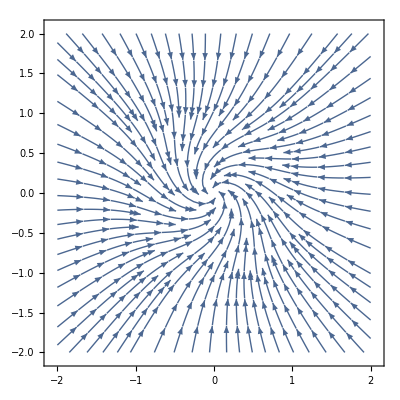

```mathematica
StreamPlot[{-x-y-x*(x^2+y^2)^2,x-y-y*(x^2+y^2)^2},{x,-2,2},{y,-2,2}]
```

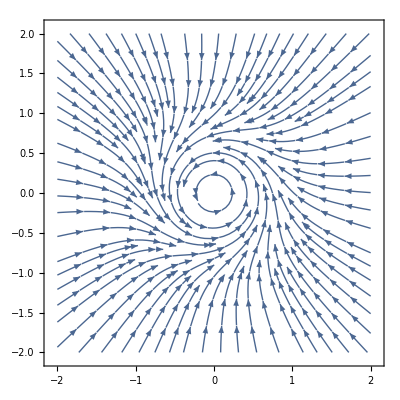

```mathematica
StreamPlot[{-y-x*(x^2+y^2)^2,x-y*(x^2+y^2)^2},{x,-2,2},{y,-2,2}]
```

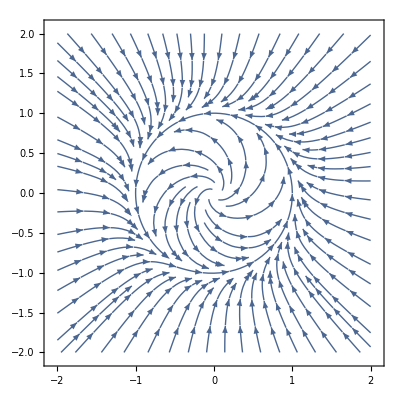

```mathematica
StreamPlot[{x-y-x*(x^2+y^2)^2,x+y-y*(x^2+y^2)^2},{x,-2,2},{y,-2,2}]
```

```mathematica
parta=StreamPlot[{x-y-x*(x^2+y^2)^2,x+y-y*(x^2+y^2)^2},{x,-2,2},{y,-2,2},StreamColorFunction->"Rainbow"];
Manipulate[Show[parta,ParametricPlot[Evaluate[First[{x[t],y[t]}/.NDSolve[{x'[t]==x[t]-y[t]-x[t]*(x[t]^2+y[t]^2)^2,y'[t]==x[t]+y[t]-y[t]*(x[t]^2+y[t]^2)^2,Thread[{x[0],y[0]}==point]},{x,y},{t,0,T}]]],{t,0,T},PlotStyle->Red]],{{T,20},1,100},{{point,{2,0}},Locator},SaveDefinitions->True]
```

```mathematica
parta=StreamPlot[{x-y-x*(x^2+y^2)^2,x+y-y*(x^2+y^2)^2},{x,-2,2},{y,-2,2},StreamColorFunction->"Rainbow"];
Manipulate[Show[parta,ParametricPlot[Evaluate[First[{x[t],y[t]}/.NDSolve[{x'[t]==x[t]-y[t]-x[t]*(x[t]^2+y[t]^2)^2,y'[t]==x[t]+y[t]-y[t]*(x[t]^2+y[t]^2)^2,Thread[{x[0],y[0]}==point]},{x,y},{t,0,T}]]],{t,0,T},PlotStyle->Red]],{{T,20},1,100},{{point,{0.5,0}},Locator},SaveDefinitions->True]
```

```mathematica
(*8ParametricPlot3D[{a,b,Solve[a+b*x-x^3==0,x，Reals]},{a,-2,2},{b,-2,2}]*)
```